# Teorija polja

1. Poiščite nivojske ploskve (ploskve kjer ima polje naprej predpisano ploskev) skalarnega polja (točki v rpostoru piredi vrednost)
	u=arcsin[z/(√(x^2+y^2))]
     in skicirajte nivojske ploskve za u=0, u=-π/2, u=π/6!

```mathematica
u=ArcSin[z/(√(x^2+y^2))]
Solve[u== k, z]
s1 = ParametricPlot3D[{r Cos[fi], r Sin[fi], r Sin[0]}, {fi,0,2Pi}, {r, 0,1}]
s2 = ParametricPlot3D[{r Cos[fi], r Sin[fi], r Sin[-Pi/2]}, {fi,0,2Pi}, {r, 0,1}]
s3 = ParametricPlot3D[{r Cos[fi], r Sin[fi], r Sin[Pi/6]}, {fi,0,2Pi}, {r, 0,1}]
Show[s1,s2,s3]
```

ArcSin[z/(√(x^2+y^2))]

{{z→ConditionalExpression[√(x^2+y^2) Sin[k],(Re[k]==-π/2&&Im[k]≥0)||-π/2<Re[k]<π/2||(Re[k]==π/2&&Im[k]≤0)]}}

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

2. Izračunajte divergenco vektorskega polja
	V⃗=1/(√(x^2+y^2))arctg(z^2-sin(x)+cos(xyz))(-x,y,z)
     v točki T(0,1,2)!

Rezultat: 4/13
Pomoč:  divV/.{x→0, y→1, z→2}	vstavi točko T(0,1,2) v splošen izraz za divV

```mathematica
?Div
```

```mathematica
u=ArcTan[z^2-Sin[x]+Cos[x y z]]/Sqrt[x^2+y^2]
V=u {-x,y,z}
Div[V, {x,y,z}]/.{x->0, y->1, z->2}
```

ArcTan[z^2+Cos[x y z]-Sin[x]]/(√(x^2+y^2))

{-(x ArcTan[z^2+Cos[x y z]-Sin[x]])/(√(x^2+y^2)),(y ArcTan[z^2+Cos[x y z]-Sin[x]])/(√(x^2+y^2)),(z ArcTan[z^2+Cos[x y z]-Sin[x]])/(√(x^2+y^2))}

4/13

3. Izračunajte rotor vektorskega polja
	V⃗=((arcsin(z/y)y)/(√(z+1)), -(ⅇ^(xz+sin(z/y))x)/(√(z+1)), √xy log(y/x))
     v točki T(2,2,0)!

Rezultat: {5,2,-1}
Pomoč: glejte nalogo 2 za izračun v dani točki.

```mathematica
?Curl
```

```mathematica
V1=ArcSin[z/y]y/Sqrt[z+1]
V2=-E^(x z +Sin[z/y])x/Sqrt[z+1]
V3=Sqrt[x y]Log[y/x]
V={V1,V2,V3}
Curl[V, {x,y,z}]/.{x-> 2, y-> 2, z-> 0}
```

(y ArcSin[z/y])/(√(1+z))

-(ⅇ^(x z+Sin[z/y]) x)/(√(1+z))

√(x y) Log[y/x]

{(y ArcSin[z/y])/(√(1+z)),-(ⅇ^(x z+Sin[z/y]) x)/(√(1+z)),√(x y) Log[y/x]}

{5,2,-1}

4. Izračunajte Δu v točki T(1,1) v polarnih je to:{r→Sqrt[2], φ→ Pi/4} , kjer je u podan v polarnih koordinatah - LAPLACE (odvod dvakrat po x + odvod dvakrat po y)
	u=ⅇ^(r sin(r φ + ln(φ+1)))arctg(φ √r).

Rezultat: -8.36069
Pomoč: če v polarnih koordinatah zapišemo u=u(r,φ), velja    !!!!!
     	Δu = (∂^2 u)/(∂r^2)+1/r(∂u)/(∂r)+1/r^2(∂^2 u)/∂^φ2

```mathematica
Clear[u,r,φ]
u=E^(r Sin[r φ+Log[φ+1]])ArcTan[φ Sqrt[r]]
D[u,r,r]+1/r D[u,r] + 1/ r^2D[u,φ, φ] /. {r->Sqrt[2], φ-> Pi/4}//N
```

ⅇ^(r Sin[r φ+Log[1+φ]]) ArcTan[√r φ]

-8.36069

# Krivuljni in ploskovni integrali

1. Najprej narišite krivuljo C, ki jo dobite kot presek
	valja x^2+y^2=1 in eliptičnega paraboloida z=x^2+2 y^2,
     nato pa izračunajte krivuljni integral
	∫_C_1 (x^2+ y) √(1+4 x^2 y^2)ⅆs,
     kjer C_1 označuje tisti del krivulje C, za katerega velja x≤0.

Rezultat: (3 π)/4

```mathematica
x=Cos[fi]
y=Sin[fi]
z=x^2 + 2 y^2
r = {x,y,z}

ParametricPlot3D[r,{fi,0,2Pi}]

ds = Norm [D[r,fi]] (* TO JE DOBRA DA NI TREBA POSEBEJ, velikost tangentnega*)
Integrate[(x^2 + y)* Sqrt[1+ 4 x^2 y^2] ds, {fi, Pi/2,3Pi/2}]
```

Cos[fi]

Sin[fi]

Cos[fi]^2+2 Sin[fi]^2

{Cos[fi],Sin[fi],Cos[fi]^2+2 Sin[fi]^2}

-Graphics3D-

√(Abs[Cos[fi]]^2+Abs[Sin[fi]]^2+4 Abs[Cos[fi] Sin[fi]]^2)

(3 π)/4

2. Dano je vektorsko polje
	V⃗={xy,xz,z^2}
     in krožnica
	C={(x,y,z); x^2+y^2=1,z=1}.
     Narišite krožnico in izračunajte krivuljni integral druge vrste
	∫_C V⃗·ⅆ r⃗    (DR zamenjamo odvod kraje vnega vektorja dt)
     Krožnica naj bo odebeljena in rdeče barve.
     
Rezultat: π

```mathematica
Clear[x,y,z]
V={x y,x z,z^2}
x=Cos[fi]
y=Sin[fi]
z=1
r= {x,y,z}
krivulja = ParametricPlot3D[r,{fi,0, 2Pi}, PlotStyle ->{Red,Thick}]

Integrate[V.D[r,fi], {fi,0,2Pi}] (*pika je skalarni produkt*)
```

{x y,x z,z^2}

Cos[fi]

Sin[fi]

1

{Cos[fi],Sin[fi],1}

-Graphics3D-

π

π

3. Prepričajte se, da je integral
	∫_A^B (-2 x y+(2 x y z^3)/(√(1-x^4 y^2 z^6)),-x^2+(x^2 z^3)/(√(1-x^4 y^2 z^6))+(cos(y/z))/z,ⅇ^z+(3 x^2 y z^2)/(√(1-x^4 y^2 z^6))-(y cos(y/z))/z^2).ⅆ r⃗
     neodvisen od integracijske poti in ga izračunajte za primer A(1,0,2), B(0,π,2). (daljica ni dobra, ker gre kje čez točko 0 in je deljenje z nič)

Rezultat: 1

```mathematica
Clear[x,y,z]
V={-2 x y+(2 x y z^3)/(√(1-x^4 y^2 z^6)), -x^2+(x^2 z^3)/(√(1-x^4 y^2 z^6))+Cos[y/z]/z, ⅇ^z+(3 x^2 y z^2)/(√(1-x^4 y^2 z^6))-(y Cos[y/z])/z^2}
Curl[V,{x,y,z}]
(*Iskanje potenciala*)
Integrate[V[[1]],x]
Integrate[V[[2]],y]
Integrate[V[[3]],z]
U[x_,y_, z_]:=-x^2 y+ArcSin[x^2 y z^3]+Sin[y/z]+ⅇ^z+k

(*Odgovor je zgolj razlika potencialov*)
U[0,Pi,2]-U[1,0,2](*KONČNA - ZAČETNA!!!!!*)
```

{-2 x y+(2 x y z^3)/(√(1-x^4 y^2 z^6)),-x^2+(x^2 z^3)/(√(1-x^4 y^2 z^6))+Cos[y/z]/z,ⅇ^z+(3 x^2 y z^2)/(√(1-x^4 y^2 z^6))-(y Cos[y/z])/z^2}

{0,0,0}

-x^2 y+ArcSin[x^2 y z^3]

-x^2 y+ArcSin[x^2 y z^3]+Sin[y/z]

ⅇ^z+ArcSin[x^2 y z^3]+Sin[y/z]

1

4. Izračunajte ploskovni integral prve vrste
	(∫∫)_S|xyz|ⅆS,
     kjer je S del paraboloida z=x^2+y^2, ki ga odreže ravnina z=1.

Rezultat: 1/420 (-1+125 √5)

-Graphics3D-

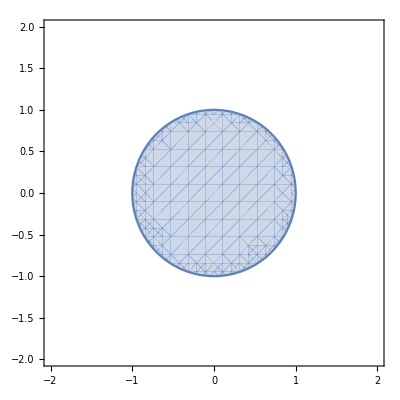

r Cos[fi]

r Sin[fi]

r^2 Cos[fi]^2+r^2 Sin[fi]^2

{r Cos[fi],r Sin[fi],r^2 Cos[fi]^2+r^2 Sin[fi]^2}

-Graphics3D-

Cos[fi]^2+Sin[fi]^2+(2 r Cos[fi]^2+2 r Sin[fi]^2)^2

0

r^2 Cos[fi]^2+r^2 Sin[fi]^2

√((r^2 Cos[fi]^2+r^2 Sin[fi]^2) (Cos[fi]^2+Sin[fi]^2+(2 r Cos[fi]^2+2 r Sin[fi]^2)^2))

1/420 (-1+125 √5)

```mathematica
Clear[x,y,z,r]
Plot3D[{x^2+y^2,1},{x,-2,2},{y,-2,2}]
RegionPlot[x^2+y^2<=1,{x,-2,2},{y,-2,2}]

x= r Cos[fi]
y=r Sin[fi]
z= x^2+y^2
s= {x,y,z}
ParametricPlot3D[s,{fi, 0,2Pi},{r,0,1}]

e=D[s,r].D[s,r]
f=D[s,r].D[s,fi]
g=D[s,fi].D[s,fi]
egf2=Sqrt[e g -f^2]
Integrate[Abs[x y z] egf2, {fi, 0,2Pi},{r,0,1}]
```

5. Preverite Stokesovo formulo za krivuljni integral iz 2. naloge, tako da izračunate ploskovni integral
	∫_S rot OverVector[V·]ⅆ S⃗,
     kjer je ploskev S 
     a) krog S={(x,y,z); z=1,x^2+y^2<1},
     b) stožec S={(x,y,z); z=√(x^2+y^2),z<1},
     c) krogelna kapica S={(x,y,z); x^2+y^2+z^2=2,z>1}.
    
     Narišite krivuljo C iz 2. naloge in posamezno ploskev S v isto sliko.
     Primerjajte dobljene rezultate z rezultatom prejšnje naloge.

```mathematica
Clear[r, x,y,z]
V={x y,x z,z^2} 
rotV = Curl[V, {x,y,z}]

(*a*)
x =r  Cos[fi]
y= r  Sin[fi]
z =1
s= {x,y,z} 

(*smer je važna, mora kazati gor *)
ploskevA = ParametricPlot3D[s, {fi,0,2 Pi}, {r,0,1}];
Show[ploskevA, krivulja]
(*mešani produkt*)
mesani=rotV.Cross[D[s,r],D[s,fi]] 

(*mešani produkt*)
Integrate[mesani, {fi,0,2Pi},{r,0,1}]




(*B*)
x =r  Cos[fi]
y= r  Sin[fi]
z =Sqrt[x^2 + y^2] (*samo parametrizacijo smo spremenili*)
s= {x,y,z} 

(*smer je važna, mora kazati gor *)
ploskevB = ParametricPlot3D[s, {fi,0,2 Pi}, {r,0,1}];
Show[ploskevB, krivulja]
(*mešani produkt*)
mesani=rotV.Cross[D[s,r],D[s,fi]] 

(*mešani produkt*)
Integrate[mesani, {fi,0,2Pi},{r,0,1}]




(*C*)
x =r  Cos[fi]
y= r  Sin[fi]
z =Sqrt[2 -x^2 - y^2]
s= {x,y,z} 

(*smer je važna, mora kazati gor *)
ploskevC = ParametricPlot3D[s, {fi,0,2 Pi}, {r,0,1}];
Show[ploskevC, krivulja]
(*mešani produkt*)
mesani=rotV.Cross[D[s,r],D[s,fi]] 

(*mešani produkt*)
Integrate[mesani, {fi,0,2Pi},{r,0,1}]
```

{x y,x z,z^2}

{-x,0,-x+z}

r Cos[fi]

r Sin[fi]

1

{r Cos[fi],r Sin[fi],1}

-Graphics3D-

(1-r Cos[fi]) (r Cos[fi]^2+r Sin[fi]^2)

π

r Cos[fi]

r Sin[fi]

√(r^2 Cos[fi]^2+r^2 Sin[fi]^2)

{r Cos[fi],r Sin[fi],√(r^2 Cos[fi]^2+r^2 Sin[fi]^2)}

-Graphics3D-

-r Cos[fi] (-(r^2 Cos[fi]^3)/(√(r^2 Cos[fi]^2+r^2 Sin[fi]^2))-(r^2 Cos[fi] Sin[fi]^2)/(√(r^2 Cos[fi]^2+r^2 Sin[fi]^2)))+(r Cos[fi]^2+r Sin[fi]^2) (-r Cos[fi]+√(r^2 Cos[fi]^2+r^2 Sin[fi]^2))

π

r Cos[fi]

r Sin[fi]

√(2-r^2 Cos[fi]^2-r^2 Sin[fi]^2)

{r Cos[fi],r Sin[fi],√(2-r^2 Cos[fi]^2-r^2 Sin[fi]^2)}

-Graphics3D-

-r Cos[fi] ((r^2 Cos[fi]^3)/(√(2-r^2 Cos[fi]^2-r^2 Sin[fi]^2))+(r^2 Cos[fi] Sin[fi]^2)/(√(2-r^2 Cos[fi]^2-r^2 Sin[fi]^2)))+(r Cos[fi]^2+r Sin[fi]^2) (-r Cos[fi]+√(2-r^2 Cos[fi]^2-r^2 Sin[fi]^2))

π

6. Izračunajte pretok polja
	V⃗=(r^2)r⃗ ,
     kjer je r⃗=(x,y,z) in r=|r⃗|, skozi ploskev
	S={(x,y,z); z=2-(x^2+y^2),z>0},
     v smeri stran od koordinatnega izhodišča.
   
    Nalogo rešite na dva načina:
    a) s ploskovnim integralom 2. vrste ∫_S OverVector[V·]ⅆ S⃗,
    b) dopolnite ploskev S do sklenjene ploskve in uporabite Gaussovo formulo.
    
Rezultat: (40 π)/3

```mathematica
Clear[x,z,y]
V=(x^2+y^2+z^2){x,y,z}
(*V naprej za primer b: *)
divV = Div[V, {x,y,z}]

x =r  Cos[fi]
y= r  Sin[fi]
z =2 -(x^2 +y^2)
s= {x,y,z} 

(*smer je važna, mora kazati gor *)
ploskev = ParametricPlot3D[s, {fi,0,2 Pi}, {r,0,Sqrt[2]}] (*z = 0 ko je r^2 = 2, glej zgoraj predpis*)

(*mešani produkt, vrstni red mora bit pravi, da kaže stran od izhodišča!*)
mesani=V.Cross[D[s,r],D[s,fi]] ;

(*mešani produkt*)
Integrate[mesani, {fi,0,2Pi},{r,0,Sqrt[2]}]




(*B: dopolnimo s krogom spodaj (alhko opazimo - avditorne: kakšno je polje da je polje na spodnji ploskvi ... kakšen je pretok skozi to ploskev? 0. Pretoka ni treba izračunati.

Če tega ne opazimo, lahko pa kar računamo.*)

x =r  Cos[fi]
y= r  Sin[fi]
z =0
s= {x,y,z} 
mesani=V.Cross[D[s,r],D[s,fi]] ; (*normala bi morala kazati "dol"*)


pretokDodan= Integrate[mesani, {fi,0,2Pi},{r,0,Sqrt[2]}]
Clear[z]
J=r (*udevemo cilindrične*)
iskaniPretok = Integrate[divV * J, {fi, 0, 2Pi}, {r, 0,Sqrt[2]}, {z,0, 2-r ^2} ] - pretokDodan
```

{x (x^2+y^2+z^2),y (x^2+y^2+z^2),z (x^2+y^2+z^2)}

5 x^2+5 y^2+5 z^2

r Cos[fi]

r Sin[fi]

2-r^2 Cos[fi]^2-r^2 Sin[fi]^2

{r Cos[fi],r Sin[fi],2-r^2 Cos[fi]^2-r^2 Sin[fi]^2}

-Graphics3D-

(40 π)/3

r Cos[fi]

r Sin[fi]

0

{r Cos[fi],r Sin[fi],0}

0

r

(40 π)/3

# Domača naloga

1. Izačunajte krivuljni integral druge vrste
	∫_C log(x y) ⅆx +y z ⅆy+ arcsin(z)x ⅆz,
     kjer C predstavlja polkrožnico
	x^2+y^2+z^2=2 x, z=x, y>0
     od točke A(0,0,0) do točke B(1,0,1).
     Krivuljo C najprej narišite!

Rezultat: 1/24 (-52+3 π+4 Log[8])

```mathematica
Clear[x,z,y]




x = t
z=t
y=  Sqrt[2x-x^2-z^2]
s= {x,y,z}  

(*smer je važna, mora kazati gor *)
krivulja= ParametricPlot3D[s, {t,0,1}] (**)
sfi=D[s,t]
V={Log[x y], y z, ArcSin[z] x}
Integrate[V.sfi,{t,0,1}]//N
```

t

t

√(2 t-2 t^2)

{t,√(2 t-2 t^2),t}

-Graphics3D-

{1,(2-4 t)/(2 √(2 t-2 t^2)),1}

{Log[t √(2 t-2 t^2)],t √(2 t-2 t^2),t ArcSin[t]}

-1.42739

```mathematica
slika1 = Plot3D[{x},{x,-10,10},{y,-5,5}]
slika2=Plot3D[{4- x^2- y^2 - x},{x,-10,10},{y,-5,5}]
Show[slika1,slika2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-